## Î(p,n)

```mathematica
hatI[p_,ν_]:= (Sqrt[π](2p)!)/(2^(2p)p!)*Gamma[(ν-2)/2]/(Gamma[(ν-1)/2+p]);
```

### Checks

```mathematica
nHatI[p_,ν_]:=NIntegrate[Sin[t]^(ν-3)*Cos[t]^(2p),{t,0,π}]
Module[{ps,ns,analy, num},
ps={0,1,2,3,4,5,10};
ns={3.9,4,4.1,4.01,π,5};
analy=Table[Table[hatI[p,n],{n,ns}],{p,ps}];
Print@analy;
Print@N@analy;
num=Table[Table[nHatI[p,n],{n,ns}],{p,ps}];
Print@num;
Print@(N@analy-num)
]
```

{{2.06422,2,1.94122,1.99389,(√π Gamma[1/2 (-2+π)])/Gamma[1/2 (-1+π)],π/2},{0.711801,2/3,0.626201,0.662422,(√π Gamma[1/2 (-2+π)])/(2 Gamma[1+1/2 (-1+π)]),π/8},{0.435797,2/5,0.368353,0.39666,(3 √π Gamma[1/2 (-2+π)])/(4 Gamma[2+1/2 (-1+π)]),π/16},{0.315795,2/7,0.259404,0.282924,(15 √π Gamma[1/2 (-2+π)])/(8 Gamma[3+1/2 (-1+π)]),(5 π)/128},{0.248378,2/9,0.199541,0.219808,(105 √π Gamma[1/2 (-2+π)])/(16 Gamma[4+1/2 (-1+π)]),(7 π)/256},{0.205083,2/11,0.16179,0.17968,(945 √π Gamma[1/2 (-2+π)])/(32 Gamma[5+1/2 (-1+π)]),(21 π)/1024},{0.110736,2/21,0.0822285,0.0938335,(654729075 √π Gamma[1/2 (-2+π)])/(1024 Gamma[10+1/2 (-1+π)]),(4199 π)/524288}}

{{2.06422,2.,1.94122,1.99389,2.86928,1.5708},{0.711801,0.666667,0.626201,0.662422,1.33979,0.392699},{0.435797,0.4,0.368353,0.39666,0.970488,0.19635},{0.315795,0.285714,0.259404,0.282924,0.790095,0.122718},{0.248378,0.222222,0.199541,0.219808,0.67931,0.0859029},{0.205083,0.181818,0.16179,0.17968,0.602843,0.0644272},{0.110736,0.0952381,0.0822285,0.0938335,0.412425,0.0251609}}

{{2.06422,2.,1.94122,1.99389,2.86928,1.5708},{0.711801,0.666667,0.626201,0.662422,1.33979,0.392699},{0.435797,0.4,0.368353,0.39666,0.970488,0.19635},{0.315795,0.285714,0.259404,0.282924,0.790095,0.122718},{0.248378,0.222222,0.199541,0.219808,0.67931,0.0859029},{0.205083,0.181818,0.16179,0.17968,0.602843,0.0644272},{0.110736,0.0952381,0.0822285,0.0938335,0.412425,0.0251609}}

{{-4.21939×10^-8,-8.88178×10^-16,1.8722×10^-8,1.50629×10^-8,-2.75335×10^-14,-1.77636×10^-15},{-1.23124×10^-13,-4.44089×10^-16,-8.60423×10^-14,9.40151×10^-9,-1.33227×10^-15,-4.44089×10^-16},{-6.66134×10^-16,-3.33067×10^-16,-1.72196×10^-13,3.73975×10^-9,-5.55112×10^-16,-2.22045×10^-16},{-4.44089×10^-16,-2.77556×10^-16,-3.33067×10^-16,1.86989×10^-9,-3.33067×10^-16,-1.52656×10^-16},{-2.30371×10^-15,-2.13718×10^-15,-1.47105×10^-15,3.7398×10^-9,-1.11022×10^-15,-4.8711×10^-15},{-3.33067×10^-16,-1.66533×10^-16,-2.22045×10^-16,1.86991×10^-9,3.88578×10^-15,-8.32667×10^-17},{3.30208×10^-13,3.32276×10^-13,3.33039×10^-13,3.3272×10^-13,2.7045×10^-13,-3.46945×10^-18}}

### comments

```mathematica
Module[{f,g},
f[p_,n_]=π/(2^(2p+n-2)(n-2))*Sum[Binomial[2p,k]Exp[I π(k-p)]/Beta[(n-1)/2+(k-p),(n-1)/2-(k-p)],{k,0,2p}];
Print[FullSimplify[f[0,n]-hatI[0,n]]];
Print[f[1,n]];
Print[hatI[1,n]];
Print[FullSimplify[f[1,n]]];
Print[FullSimplify[hatI[1,n]]];
Print[FullSimplify[f[1,n]-hatI[1,n]]];
Print[];
Print[f[2,n]];
Print[FullSimplify[f[2,n]]];
Print[FullSimplify[hatI[2,n]]];
Print[FullSimplify[f[2,n]-hatI[2,n]]];
Print[];
Print[FullSimplify[f[3,n]-hatI[3,n]]];
Print[FullSimplify[f[4,n]-hatI[4,n]]];
]
```

0

(2^(2-n) π Gamma[-1+n])/((-3+n) (-2+n) Gamma[1/2 (-3+n)] Gamma[(1+n)/2])

(√π Gamma[n/2])/(2 (-2+n) Gamma[1+1/2 (-1+n)])

(√π Gamma[-1+n/2])/(4 Gamma[(1+n)/2])

(√π Gamma[-1+n/2])/(4 Gamma[(1+n)/2])

0

(3 2^(2-n) π Gamma[-1+n])/((-5+n) (-3+n) (-2+n) Gamma[1/2 (-5+n)] Gamma[(3+n)/2])

(3 √π Gamma[-1+n/2])/(8 Gamma[(3+n)/2])

(3 √π Gamma[-1+n/2])/(8 Gamma[(3+n)/2])

0

0

0

```mathematica
Module[{a,n},
(*a=(3*1*(-1)/((3!)^2)-2*3*(-3)/4!/2!+2*3*(-5)*(-3)/5!-2/6!(-3)(-5)(-7))*6!;
Print@a;
Print@FactorInteger[a];


a=(
(5*3*1*(-1))/((4!)^2)-2/5!/3!*(5*3*1)((-3))+2/6!/2!(5*3)((-3)(-5))-2/7!/1!(5)((-3)(-5)(-7))+2/8!/0!*((-3)(-5)(-7)(-9))
)*8!;
Print@a;
Print@FactorInteger[a];*)

n[p_]:=(Sow[1/((p!)^2)Pochhammer[-1/2,p],"0"]
+2Sum[
Sow[(-1)^(l)/((p+l)!(p-l)!),"l"]
*Sow[(Pochhammer[-1/2+l,p-l]),"a"]
*Sow[( Pochhammer[-1/2-l,l]),"b"],
{l,p}])*(p)!(*/2^(p)*);
Print@Reap@n[0];
Print@Reap@n[1];
Print@FactorInteger@n[2];
Print@FactorInteger@n[3];
Print@FactorInteger@n[4];
Print@FactorInteger@n[5];
Print@FactorInteger@n[6];
]
```

{1,{{1}}}

{1,{{-1/2},{-1/2},{1},{-3/2}}}

{{1,1}}

{{1,1}}

{{1,1}}

«2 more identical outputs»

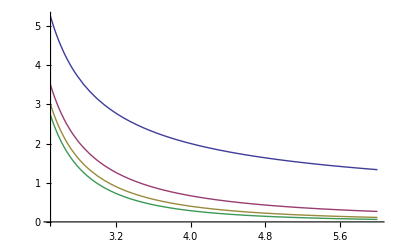

```mathematica
Plot[Evaluate[Table[hatI[p,n],{p,0,3}]],{n,2.5,6}]
```

## -k,-l ∈ Ν_0

### Check to hep-ph 0005120 and Phys.Rev.D40.54

```mathematica
FullSimplify[hatI[0,n-1]*hatI[0,n]]
```

(2 π)/(-3+n)

```mathematica
FullSimplify[(a^2hatI[0,n]+b^2 hatI[1,n])*hatI[0,n-1]]
```

(2 (b^2+a^2 (-1+n)) π)/((-3+n) (-1+n))

```mathematica
FullSimplify[(A^2hatI[0,n]+B^2 hatI[1,n])*hatI[0,n-1] + C^2 hatI[1,n-1]hatI[0,n+2]]
```

(2 (B^2+C^2+A^2 (-1+n)) π)/((-3+n) (-1+n))

```mathematica
FullSimplify[(a A hatI[0,n]+b B hatI[1,n])*hatI[0,n-1]]
```

(2 (b B+a A (-1+n)) π)/((-3+n) (-1+n))

## singular a, k,-l ∈ Ν

### Check to hep-ph 0005120 and Phys.Rev.D40.54

```mathematica
FullSimplify[hatI[0,n-1]*hatI[0,n-2]]
```

(2 π)/(-4+n)

```mathematica
FullSimplify[hatI[0,n-1]*(hatI[0,n-4]+hatI[1,n-4])]
```

(2 π)/(-6+n)

```mathematica
FullSimplify[hatI[0,n-1]*(A hatI[0,n-2]+B hatI[1,n-2])]
FullSimplify@Series[hatI[0,n-1]*(A hatI[0,n-2]+B hatI[1,n-2])/.{n-> 4+ϵ},{ϵ,0,0}]
```

(2 (B+A (-3+n)) π Gamma[-4+n])/Gamma[-2+n]

(2 (A+B) π)/ϵ-2 (B π)+O[ϵ]^1

### comments

```mathematica
hatI[0,3+ϵ]
```

(2 √π Gamma[(3+ϵ)/2])/((1+ϵ) Gamma[(2+ϵ)/2])

```mathematica
FullSimplify@Integrate[Sin[t]^(ν-3)/(a+a Cos[t]),{t,0,π}]
```

ConditionalExpression[1/(32 a)ⅇ^(-1/2 ⅈ π ν) √π (-(32 Cos[(π ν)/2] Gamma[-3+ν])/Gamma[-5/2+ν]+(4 π (ⅈ (-2+ν)+4 (-3+ν) Cot[(π ν)/2]))/(Gamma[3-ν/2] Gamma[1/2 (-1+ν)])+2^ν √π Csc[(π ν)/2] (ν HypergeometricPFQ[{1-ν/2},{},1]-(-5+ν) HypergeometricPFQ[{-ν/2},{},1])),Re[ν]>4]

```mathematica
FullSimplify[hatI[0,3+ϵ]*Integrate[Sin[t]^(1+ϵ)/(1+Cos[t]),{t,0,π}]]
```

ConditionalExpression[(2 π)/ϵ,Re[ϵ]>0]

```mathematica
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t],{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^2,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^3,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^4,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^6,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^8,{t,0,π}]
```

ConditionalExpression[-(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[-(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(15 √π Gamma[ϵ/2])/(8 Gamma[(7+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(105 √π Gamma[ϵ/2])/(16 Gamma[(9+ϵ)/2]),Re[ϵ]>0]

```mathematica
FullSimplify[(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2])-(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2])]
```

(√π Gamma[1+ϵ/2])/(2 Gamma[(5+ϵ)/2])

```mathematica
hatI[0,ν-2]
FullSimplify@hatI[0,ν-2]
```

(2 √π Gamma[1/2 (-2+ν)])/((-4+ν) Gamma[1/2 (-3+ν)])

(√π Gamma[-2+ν/2])/Gamma[1/2 (-3+ν)]

```mathematica
hatI[1,4+ϵ]
```

(√π Gamma[(4+ϵ)/2])/((2+ϵ) Gamma[1+(3+ϵ)/2])

```mathematica
hatI[1,2+ϵ]
```

(√π Gamma[(2+ϵ)/2])/(ϵ Gamma[1+(1+ϵ)/2])

```mathematica
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^k,{t,0,π}]
```

ConditionalExpression[(2^(k+ϵ) π Csc[k π+(π ϵ)/2] Gamma[1+ϵ/2] Hypergeometric2F1Regularized[-k,-k-ϵ,1-k-ϵ/2,1/2])/Gamma[1+k+ϵ]+2^(ϵ/2) Gamma[1+k] Gamma[ϵ/2] Hypergeometric2F1Regularized[-ϵ/2,ϵ/2,1+k+ϵ/2,1/2] ((-1)^k-Csc[k π+(π ϵ)/2] Sin[(π ϵ)/2]),Re[ϵ]>0]

```mathematica
Integrate[1/(a+b x),x]
```

Log[a+b x]/b

```mathematica
Sum[(-b/a)^(2p)(2p)!/(2^(2p-1)p!Gamma[(ν-1)/2+p]),{p,∞}]
```

(b^2 Hypergeometric2F1[1,3/2,(1+ν)/2,b^2/a^2])/(a^2 Gamma[(1+ν)/2])

```mathematica
Sum[(2p)!/(2^(2p-1)p!Gamma[(ν-1)/2+p]),{p,∞}]
```

Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])

```mathematica
FullSimplify[Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])Sqrt[π]/a Gamma[ν/2]/(ν-2)]
```

(2^(-3+ν) Gamma[-2+ν/2] Gamma[ν/2])/(a Gamma[-1+ν])

```mathematica
FullSimplify[(2^(-3+ν) Gamma[-2+ν/2] Gamma[ν/2])/(a Gamma[-1+ν])-Sqrt[π]/(2a )Gamma[(ν-4)/2]/Gamma[(ν-1)/2]]
```

0

```mathematica
Series[FullSimplify[Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])Sqrt[π]/a Gamma[ν/2]/(ν-2)]/.{ν-> 4+ϵ},{ϵ,0,2}]
```

2/(a ϵ)+(2 (-1+Log[2]))/a+((24-π^2-24 Log[2]+12 Log[2]^2) ϵ)/(12 a)+((-32+2 π^2+48 Log[2]-2 π^2 Log[2]-24 Log[2]^2+8 Log[2]^3+PolyGamma[2,1]+PolyGamma[2,2]-8 PolyGamma[2,3]) ϵ^2)/(24 a)+O[ϵ]^3

```mathematica
Series[(Sqrt[π]/(2a )Gamma[(ν-4)/2]/Gamma[(ν-1)/2])/.{ν-> 4+ϵ},{ϵ,0,2}]
```

2/(a ϵ)+(-EulerGamma-PolyGamma[0,3/2])/a+((12+3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,3/2]+3 PolyGamma[0,3/2]^2) ϵ)/(12 a)+1/(24 a)(-12 EulerGamma-EulerGamma^3+EulerGamma π^2-12 PolyGamma[0,3/2]-3 EulerGamma^2 PolyGamma[0,3/2]+π^2 PolyGamma[0,3/2]-3 EulerGamma PolyGamma[0,3/2]^2-PolyGamma[0,3/2]^3+PolyGamma[2,1]-PolyGamma[2,3/2]) ϵ^2+O[ϵ]^3